# Lower bound ρ and λ for circles

## Set up

We place circles that rest on the x-axis. The target is on the positive x-axis

Set the initial circle circ(x, r=y)

```mathematica
c=circ[0.,1.];
```

Set the distance of the target

```mathematica
t=100.
```

100.

Define a function that can draw these circles

## Helper functions

This translates our internal circle to a graphics primitive that can be drawn

```mathematica
showCircle[circ[x_,r_]]:=Disk[{x,r},r]
```

This rotates a point P clockwise around a point O with an angle θ.

```mathematica
rotate[P:{_,_},O:{_,_},θ_]:=({{Cos[θ], Sin[θ]}, {-Sin[θ], Cos[θ]}}).(P-O)+O
```

```mathematica
P1={12,5};Piv={3,3};
rot=Table[rotate[P1,Piv,n Degree],{n,0,330,30}]//N;
Graphics[{PointSize[Large],Point@Piv,Gray,Point/@rot}]
```

-Graphics-

## Starting point

Find the point where the robot starts to follow a circle:
If O is the origin of a circle Γ with O_x<T_x, this finds the intersection of OT with the Γ that is furthest away from T.
We obtain this point by taking the point Q where the x-axis touches Γ. We can then rotate clockwise by 90° + ∠OTQ to get the point we are looking for

```mathematica
sp[Γ_,Tx_]:=Module[{T,x,y,r,angle,Q},
T={Tx,0};
{x,y}=List@@Γ;r=y;
angle=ArcTan[Tx-x,y];
Q={x,0};
rotate[Q,List@@Γ,90°+angle]
];
```

```mathematica
sp[c,t]
```

{-0.99995,1.01}

## Leave point

Similarly, from symmetry considerations, we can find the point where the robot leave the circle again

```mathematica
lp[Γ_,Tx_]:=Module[{T,x,y,r,angle,Q},
T={Tx,0};
{x,y}=List@@Γ;r=y;
angle=ArcTan[Tx-x,y];
Q={x,0};
 rotate[Q,List@@Γ,180°+2angle]
];
```

```mathematica
lp[c,t]
```

{0.019998,1.9998}

## Arc

Similarly again, this returns the circle arc that was follows on a circle 
(we have to define it counter-clockwise, now)

```mathematica
arc[Γ_,Tx_]:=Module[{T,x,y,r,angle},
T={Tx,0};
{x,y}=List@@Γ;r=y;
angle=ArcTan[Tx-x,y];
Circle[{x,y},r,{180°-angle,90°-2angle}]
]
```

```mathematica
arc[c,t]
```

Circle[{0.,1.},1.,{3.13159,1.5508}]

The length of the arc is

```mathematica
arclength[Circle[O:{_,_},r_,{α0_,α1_}]]:=
r Abs[α0-α1]
```

```mathematica
arclength[arc[c,t]]
```

1.5808

```mathematica
linelength[Line[{a:{_,_},b:{_,_}}]]:=Norm[a-b]
```

## Next circle

This finds the next circle based on the previous

```mathematica
(* Next circle *)
nc[Null,Tx_]:=Null;
nc[prev_,Tx_]:=Module[{Px,Py,Lx,Ly,Ox,Oy,OxA,OyA,discr},
{Px,Py}=List@@prev;
{Lx,Ly}=lp[prev,Tx];
discr=Ly^3 Py (Lx Px+Ly Py-Lx Tx-Px Tx+Tx^2);
If[discr≥0,
Ox=(Lx Ly Px+2 Ly^2 Py-Ly Px Tx-2 √discr)/(Lx Ly-Ly Tx); OxA=(Lx Ly Px+2 Ly^2 Py-Ly Px Tx+2 √discr)/(Lx Ly-Ly Tx);
Oy=(Ly (Ox-Tx))/(Lx-Tx);OyA=(Ly (OxA-Tx))/(Lx-Tx);
If[Oy>0&&Abs[Tx-Ox]≤Abs[Tx-Px],circ[Ox,Oy],Null],
Null]
];
```

## Drawing & Simulation

Define my favourite color:

```mathematica
bada55=RGBColor[186/255,218/255,85/255];
```

Manipulate target distance:

```mathematica
Manipulate[
circles=NestList[nc[#,t]&,c,100];
circles=DeleteCases[circles,Null];

startings=sp[#,t]&/@circles;
leavings=lp[#,t]&/@circles;
arcs=arc[#,t]&/@circles;
pieces=Table[Line[{leavings[[ii]],startings[[ii+1]]}],{ii,1,Length[startings]-1}];

Opt=N[t+π/2];
R=Total[arclength/@arcs]+Total[linelength/@pieces];
ratio=R/Opt;
(* PlotLabel->Style["t = "<>ToString[t]<>",     N_circles = "<>ToString[Length[circles]]<>",     |R(S,T)|/|O(S,T)| = "<>ToString[ratio],FontFamily->"Skolar PE"] *)
Graphics[{
Lighter[LightGray,.3],showCircle/@circles,Thick,RGBColor[0,150/255,214/255],pieces,arcs,
bada55,Line[{{0,0},{t,0}}],
PointSize[Large],RGBColor[.7,.3,.2],Point[{t,0}]
},ImageSize->800]
,{{t,20},10,100000}]
```

Make a table of the ratios:

```mathematica
ratios=Table[
circles=NestList[nc[#,t]&,c,100];
circles=DeleteCases[circles,Null];

startings=sp[#,t]&/@circles;
leavings=lp[#,t]&/@circles;
arcs=arc[#,t]&/@circles;
pieces=Table[Line[{leavings[[ii]],startings[[ii+1]]}],{ii,1,Length[startings]-1}];

Opt=N[t+π/2];
R=Total[arclength/@arcs]+Total[linelength/@pieces];
ratio=R/Opt,
{t,10,10000}];
```

Power::infy: Infinite expression 1/0. encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

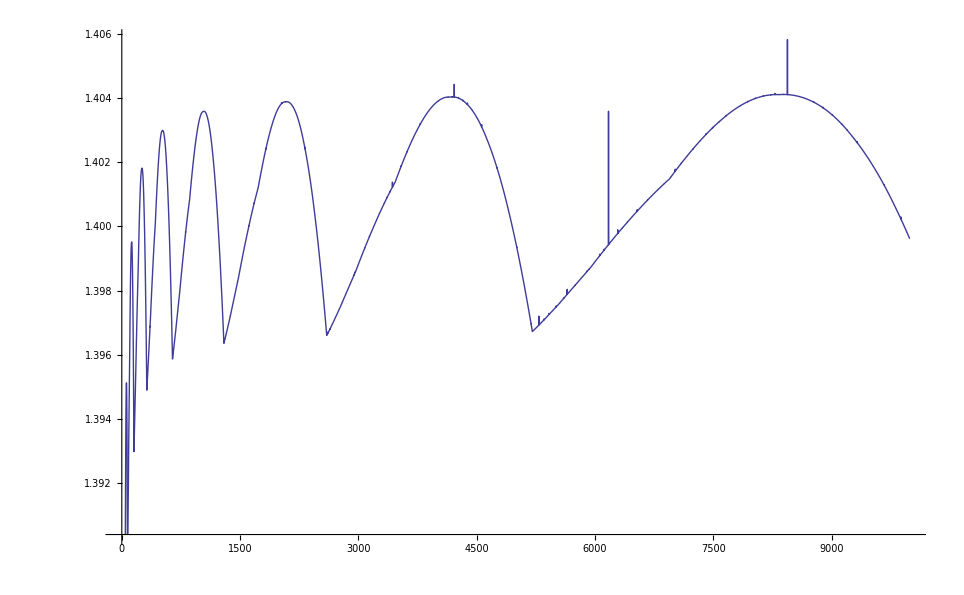

```mathematica
ListLinePlot[ratios]
```